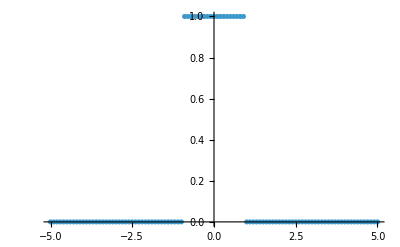

```mathematica
targetData = Table[{x,If[Abs[x]<1,1,0]},{x,-5,5,0.1}];
ListPlot[targetData]
```

```mathematica
n = 20;
expr = Sum[Subscript[a, i]*Exp[-x^2/(2 Subscript[σ, i]^2)],{i,1,n}]
coeffs = Flatten[Table[{Subscript[a, i],Subscript[σ, i]},{i,1,n}]]

nlm=NonlinearModelFit[
targetData,
expr,
coeffs,
x,
(*Method->{"NMinimize","Method"->"NelderMead"}*)
Method->"NMinimize"
]
```

ⅇ^(-x^2/(2 σ_1^2)) a_1+ⅇ^(-x^2/(2 σ_2^2)) a_2+ⅇ^(-x^2/(2 σ_3^2)) a_3+ⅇ^(-x^2/(2 σ_4^2)) a_4+ⅇ^(-x^2/(2 σ_5^2)) a_5+ⅇ^(-x^2/(2 σ_6^2)) a_6+ⅇ^(-x^2/(2 σ_7^2)) a_7+ⅇ^(-x^2/(2 σ_8^2)) a_8+ⅇ^(-x^2/(2 σ_9^2)) a_9+ⅇ^(-x^2/(2 σ_10^2)) a_10+ⅇ^(-x^2/(2 σ_11^2)) a_11+ⅇ^(-x^2/(2 σ_12^2)) a_12+ⅇ^(-x^2/(2 σ_13^2)) a_13+ⅇ^(-x^2/(2 σ_14^2)) a_14+ⅇ^(-x^2/(2 σ_15^2)) a_15+ⅇ^(-x^2/(2 σ_16^2)) a_16+ⅇ^(-x^2/(2 σ_17^2)) a_17+ⅇ^(-x^2/(2 σ_18^2)) a_18+ⅇ^(-x^2/(2 σ_19^2)) a_19+ⅇ^(-x^2/(2 σ_20^2)) a_20

{a_1,σ_1,a_2,σ_2,a_3,σ_3,a_4,σ_4,a_5,σ_5,a_6,σ_6,a_7,σ_7,a_8,σ_8,a_9,σ_9,a_10,σ_10,a_11,σ_11,a_12,σ_12,a_13,σ_13,a_14,σ_14,a_15,σ_15,a_16,σ_16,a_17,σ_17,a_18,σ_18,a_19,σ_19,a_20,σ_20}

FittedModel[…]

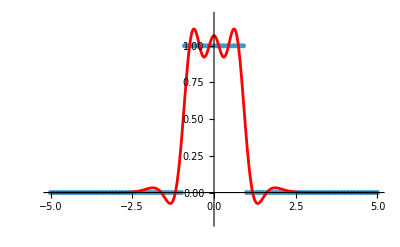

```mathematica
Show[
ListPlot[targetData,PlotRange->{-0.2,1.2}],
Plot[nlm["BestFit"],{x,-5,5},PlotStyle->Red]

]
```

```mathematica
nlm["BestFitParameters"]
```

{a_1→-28.4105,σ_1→-0.387493,a_2→17.7973,σ_2→-0.455716,a_3→-22.1689,σ_3→-0.54456,a_4→16.7822,σ_4→0.455535,a_5→17.7365,σ_5→0.455437,a_6→17.3506,σ_6→0.343742,a_7→19.7334,σ_7→0.343735,a_8→-21.9363,σ_8→0.544162,a_9→17.5375,σ_9→-0.455697,a_10→15.5191,σ_10→0.455559,a_11→17.0646,σ_11→-0.455716,a_12→-22.1975,σ_12→-0.544569,a_13→20.2182,σ_13→0.343742,a_14→-28.0239,σ_14→0.387277,a_15→-29.5147,σ_15→0.387303,a_16→-28.8113,σ_16→-0.387526,a_17→16.6655,σ_17→0.455374,a_18→16.7649,σ_18→0.622958,a_19→-28.653,σ_19→-0.387501,a_20→17.615,σ_20→0.455455}